```mathematica
Quit[]
```

# Axion Stars and Gravitational Atoms

For further details, see:
Banerjee, Budker, Eby, Kim, and Perez, “Relaxion Stars and their Detection via Atomic Physics”. Communications Physics volume 3, Article number: 1 (2020). [arXiv: 1902.08212]

# Setup

### Basics

#### Style

```mathematica
frameLabelSize=1.5;
linethickness=0.003;
thinlinethickness=0.002;
frameticksSize=15;
```

```mathematica
<<MaTeX`

SetOptions[MaTeX,"Preamble"->{"\\usepackage[dvipsnames]{xcolor}"}];
tex[a_,b_]:=MaTeX[a,Magnification->b];
tex15[a_]:=MaTeX[a,Magnification->1.5];

(* BaseStyle->{FontFamily->"Latin Modern Math"} *) 
mysty={BaseStyle->{FontFamily->"Latin Modern Math",FontColor->Black},
FrameStyle->BlackFrame,
Frame->True,
Axes->False};

ticks=Flatten[
Join[Table[Join[{{10^j,StringForm["10^(``)",j],{0.02,0}}},Table[{i*10^j,"",{0.008,0}},{i,2,9}]],{j,-30,30}]],1];

ticksNoLabel=Flatten[
Join[Table[Join[{{10^j,StringForm["",j],{0.02,0}}},Table[{i*10^j,"",{0.008,0}},{i,2,9}]],{j,-30,30}]],1];

ticksEven=Flatten[
Join[Table[Join[{{10^j,If[Mod[j,2]==0,StringForm["10^(``)",j],""],{0.02,0}}},Table[{i*10^j,"",{0.008,0}},{i,2,9}]],{j,-50,20}]],1];

ticksOdd=Flatten[
Join[Table[Join[{{10^j,If[Mod[j,2]==1,StringForm["10^(``)",j],""],{0.02,0}}},Table[{i*10^j,"",{0.008,0}},{i,2,9}]],{j,-50,20}]],1];
```

#### Constants

```mathematica
(* 648000/Pi is unit conversion from radian to arcsec *)
radtoarcsec=π/648000;

(* Unit conversion *)
mGeV=(1.9733*^-16 )^-1;             (* 1 GeV = # m^-1 *)
cmGeV=(1.9733 * 10^-14)^-1;           (* 1 GeV = # cm^-1*)
gGeV=(1.7827 * 10^-24)^-1;             (* 1 GeV = # g *)
secGeV=(6.5822 * 10^-25)^-1;         (* 1 GeV = # sec^-1 *)

secperyear=365(*.25*)*24*60*60; (* 1 year = # sec *)

(* -----------------------------------------------------------------*)

(*                             Mass scale                        *)
(*                     All written in GeV unit                   *)
Mpl=1.22 10^19;                                   (* Mpl = non-reduced Planck mass  *)
me= 0.511 10^-3;                                  (* me = electron mass             *)
mh=125;                                                   (* mh = Higgs mass                *)
v=246;                                                     (* v = Higgs vev                   *)
ME=3.3499747573904756 10^51;      (* ME = Earth mass                *)
Msun=1.1160000000000002 10^57 ; (* Msun = Solar mass              *)

(* -----------------------------------------------------------------*)

(* virial velocity in the galaxy, units of cLight *)
vvir=10^-3;

(* speed of light, m/sec *)
cLight=2.997 10^8;

(* fine structure constant, central value *)
alpha=1/137.;

(* electron yukawa *)
ye=me/mh;

(* low energy higgs to gamma gamma coupling *)
(* assuming the higgs mass is very small    *)
(* in GeV^-1 Unit                             *)
ghg=alpha/(2Pi v);

(* -----------------------------------------------------------------*)

(*                     Length scale                           *)
(*          all length scale written in [m] unit              *)
RE=6371 10^3.;                 (* RE = Earth radius                    *)
RMoon=3.8 10^8;              (* RMoon = distance from us to Moon     *)
RLAGEOS=1.23 10^7;       (* RLAGEOS = distance from us to LAGEOS *)
Rsun = 695508 10^3;       (* Rsun = sun radius      *)
AU=149597870695.88; (* AU = Astronomical unit *)

(* -----------------------------------------------------------------*)

(*                     Density scale                           *)
(*   All written in [GeV^4] unit (unless otherwise specified)   *)
rlocal=3.07 10^-42;         (* local DM density *)
rEarth=(4π)/3 ME/(RE^3 mGeV^3);      (* earth density *)

rlocalkgkm3=rlocal*(mGeV^3 10^-3)/(gGeV 10^-9)(* kg/km^3 *);
```

# Calculations

## Axion Star Parameters

### Physical Parameters

```mathematica
(* geometric cross section of relaxion star with Earth [km^2]   *)
σHit=π Rkm^2;

(* rate of encounters between relaxion star and Earth [1/year] *)
Γlocal=rlocalkgkm3/Mkg σHit(vvir cLight/10^3) secperyear ;

(* relaxion star density [kg/km^3]                             *)
ρAStkgkm3=Mkg/(7π Rkm^3);

(* relaxion star overdensity relative to local DM background  *)
overdensity=ρAStkgkm3/rlocalkgkm3 ;

(* maximum stable relaxion star mass [kg]                     *)
Mmax=10.15 ((Mpl (10^3 gGeV)^-1)fGeV)/(meV 10^-9);
```

```mathematica
(* mass-radius relation for stable boson star *)
MkgASt[meV_,Rkm_]:=Mpl^2/((meV 10^-9)^2)2/(Rkm (10^3 gGeV)(10^3 mGeV))
```

```mathematica
(* radial scales, all measured in km  *)

(* Relaxion star radius, gravitationally stable configuration *)
RkmASt[meV_,Mkg_]:=Mpl^2/((meV 10^-9)^2)2/Mkg 1/((10^3 gGeV)(10^3 mGeV))

(* Relaxion star radius, border of gravitationally unstable region  *)
RkmUNSTABLE[fsub_,Mkg_]:=(RkmASt[meV,Mkg]/.Solve[Mmax==Mkg,meV]⟦1⟧)/.fGeV->fsub//Quiet (* fix Subscript[m, ϕ] by the maximum mass relation and show R vs M along the unstable line *)

(* DM object radius at fixed density ρ *)
RkmFIXρ[ρsub_,Mkg_]:=Rkm/.Solve[(ρAStkgkm3)==ρsub,Rkm]⟦3⟧//Quiet(* select the unique root that is real and positive *)

(* DM object radius at fixed encounter rate Γ *)
RkmFIXΓ[Γsub_,Mkg_]:=Rkm/.Solve[Γlocal==Γsub,Rkm]⟦2⟧//Quiet
(* select the unique root that is positive *)
```

```mathematica
(* Fix Γ = 1/year, deterimine overdensity and critical density *)

(* Write M = Subscript[M, max]/x for x≥1; determine x such that Γ = 1/year *)
xatΓ1=x/.Solve[(Γlocal/.Rkm->RkmASt[meV,Mkg]/.Mkg->Mmax/x)==1.,x]⟦3⟧//Quiet;

(* Determine δ such that Γ = 1/year (depends only on Subscript[m, ϕ]) *)
δatΓ1=overdensity/.Rkm->RkmASt[meV,Mkg]/.Mkg->Mmax/xatΓ1;

(* Subscript[m, ϕ] such that δ = 1,10^3,10^6 *)
matδ1=meV/.Solve[δatΓ1==1,meV]⟦1⟧;
matδ3=meV/.Solve[δatΓ1==10^3,meV]⟦1⟧;
matδ6=meV/.Solve[δatΓ1==10^6,meV]⟦1⟧;

(* Determine f [GeV] such that x=1 (i.e. M=Subscript[M, max]) and Γ = 1/year *)
fatx1=fGeV/.Solve[xatΓ1==1.,fGeV]⟦1⟧;
```

## Gravitational Atom Parameters

### Mass, Radius, and Density

```mathematica
(*                    Gravitational Atom Radius                   *)
(*   Rhalo [meter] hosted by massive body of mass Mext [GeV] *)
RhaloNaive[meV_,Mext_]:=(Mpl^2/((meV 10^-9)^2)*1/Mext)1/mGeV; (* assuming central mass is point-like *)

Rhalo[meV_,Mext_,Rext_]:=Max[(Mpl^2/((meV 10^-9)^2)*1/Mext)1/mGeV,(Mpl^2/((meV 10^-9)^2)*(Rext)^3/(Mext mGeV))^(1/4)];

RhaloEarth[meV_]:=Rhalo[meV,ME,RE]; (* hosted by Earth *)
RhaloSun[meV_]:=Rhalo[meV,Msun,Rsun]; (* hosted by Earth *)
```

```mathematica
(*           Gravitational Atom density profile              *)
(* rhoOut    = when r > Subscript[R, ext] [hydrogen atom]                  *)
(* rhoIn     = when r < Subscript[R, ext] [harmonic oscillator]            *)
(* rho       = if R_* > Subscript[R, ext] take rhoOut, otherwise take rhoIn *)
(* rhoSewing = smoothly stitch two profiles at r=Subscript[R, ext]         *)

(* dimensionless density profile ((R_*)^3/M_*)ρ_*                    *)
DIMrhoOut[meV_,Mext_,Rext_,r_]:=(1/π)*Exp[(-2r)/Rhalo[meV,Mext,Rext]];
DIMrhoIn[meV_,Mext_,Rext_,r_]:=(1/π^(3/2))*Exp[-(r/Rhalo[meV,Mext,Rext])^2];

DIMrhoSewing[meV_,Mext_,Rext_,r_]:=
If[Rhalo[meV,Mext,Rext]>Rext,
DIMrhoOut[meV,Mext,Rext,r],
DIMrhoIn[meV,Mext,Rext,r]HeavisideTheta[Rext-r]+DIMrhoIn[meV,Mext,Rext,Rext]/DIMrhoOut[meV,Mext,Rext,Rext]*DIMrhoOut[meV,Mext,Rext,r]HeavisideTheta[r-Rext]];

(* dimensionful density profile in GeV^4                     *)

rhoOut[meV_,Mstar_,Mext_,Rext_,r_]:=(Mstar/mGeV^3)/Rhalo[meV,Mext,Rext]^3*DIMrhoOut[meV,Mext,Rext,r];

rhoIn[meV_,Mstar_,Mext_,Rext_,r_]:=(Mstar/mGeV^3)/Rhalo[meV,Mext,Rext]^3*DIMrhoIn[meV,Mext,Rext,r];

rho[meV_,Mstar_,Mext_,Rext_,r_]:=If[Rhalo[meV,Mext,Rext]>Rext,
rhoOut[meV,Mstar,Mext,Rext,r],
rhoIn[meV,Mstar,Mext,Rext,r]];

rhoSewing[meV_,Mstar_,Mext_,Rext_,r_]:=(Mstar/mGeV^3)/Rhalo[meV,Mext,Rext]^3*DIMrhoSewing[meV,Mext,Rext,r];

(* scalar field profile ϕ=(√(2ρ))/Subscript[m, ϕ] [GeV]
for halo density ρ [GeV^4] 
and axion mass Subscript[m, ϕ] [eV] *)

phiHaloProfile[meV_,Mstar_,Mext_,Rext_,r_]:=(√(2rho[meV,Mstar,Mext,Rext,r]))/(meV*10^-9);
```

```mathematica
rhoEarth[meV_,Mstar_,r_]:=rho[meV,Mstar,ME,RE,r]; (* hosted by Earth *)
rhoSun[meV_,Mstar_,r_]:=rho[meV,Mstar,Msun,Rsun,r]; (* hosted by Sun *)

phiHaloProfileEarth[meV_,Mstar_,r_]:=phiHaloProfile[meV,Mstar,ME,RE,r]; (* hosted by Earth *)
phiHaloProfileSun[meV_,Mstar_,r_]:=phiHaloProfile[meV,Mstar,Msun,Rsun,r]; (* hosted by Sun *)
```

### Gravitational Constraints

#### ...on Earth Halo, from orbit of Moon and LAGEOS satellite (Adler ‘08)

```mathematica
(* constrained mass enclosed between LAGEOS and Moon *)
Mcon=4 10^-9 ME;

(* cutoff for consistency, M_* < 1/2 Subscript[M, ext] *)
MstarCut=1/2.;

(* Maximally allowed axion Earth halo mass (from Adler '08) *)
MmaxADLER[meV_]:=Mcon/(4π)*(NIntegrate[r^2 DIMrhoSewing[meV,ME,RE,r RhaloEarth[meV]],{r,(RLAGEOS/RhaloEarth[meV]),(RMoon/RhaloEarth[meV])}])^-1

(* Maximally allowed axion Earth halo mass *)
MmaxEarth[meV_]:=Min[MmaxADLER[meV]/ME,MstarCut]*ME;
```

#### ...on Solar Halo, from Solar System Ephemerides (Pitjev and Pitjeva ‘13)

```mathematica
(*           semi-major axis a [meters], 
                    eccentricity e, 
             and orbital period T [years]       *)
(* Mercury, Venus, Earth, Mars, Jupiter, Saturn *)
aPlanets={0.387098,0.723,1,1.524,5.2044,9.0412}AU;
ePlanets={0.205630,0.007,0.0167,0.0934,0.0489,0.0565};
TPlanets={87.9691/365,224.7/365,1,1.881,11.862,29.4571};

(* Pitjev and Pitjeva result, precession per year *)
Pitev13={0.000030,0.000016,0.0000019,0.00000037,0.000283,0.0000047};

(* rate of change in perihelion per year *)
(* rdm = dark matter density in g/m^3    *)
pidot[rdm_]:=(4 π^2*(aPlanets)^3(1-ePlanets^2)^(1/2)rdm)/((Msun/gGeV) TPlanets radtoarcsec);

(* constraints on rho_dm [g] at each planet's orbital radius *)
rhomaxPP=Pitev13/pidot[rdm] rdm;

(* Maximally allowed axion Solar halo mass (from Pitjev & Pitjeva '08) *)
MmaxPP[meV_]:=(rhomaxPP*(π #2^3 Exp[2#1/#2])* gGeV)&[aPlanets,Rhalo[meV,Msun,Rsun]]

(* Maximally allowed axion Solar halo mass *)
MmaxSun[meV_]:=Min[MmaxPP[meV]/Msun,MstarCut]*Msun;
```

# Example Figures

## Axion Star Encounter Rates

### Encounter Rate: 1/year. Plot f vs m_ϕ

#### Range

```mathematica
logticks1=Flatten[Table[{i 10^(1+k),If[i==1&&EvenQ[k],i*Superscript[10,1+k],""]},{k,3,20},{i,1,9}],1];
logticks2=Flatten[Table[{i 10^(1+k),If[i==1&&EvenQ[k],i*Superscript[10,1+k],""]},{k,-14,0},{i,1,9}],1];

(* Plot range options *)
mmin=10^-13;
mmax=1;

fmin=10^7;
fmax=Mpl;
```

#### Separate Plots

```mathematica
(* (Vertical) Lines of fixed δ in f vs Subscript[m, ϕ] plane *)
line1=Line[{{Log[matδ1],Log[fatx1/.meV->matδ1]},{Log[matδ1],Log[10^20.]}}];
line2=Line[{{Log[matδ3],Log[fatx1/.meV->10^4.5 matδ1]},{Log[matδ3],Log[10^20.]}}];
line3=Line[{{Log[matδ6],Log[fatx1/.meV->10^9 matδ1]},{Log[matδ6],Log[10^20.]}}];
```

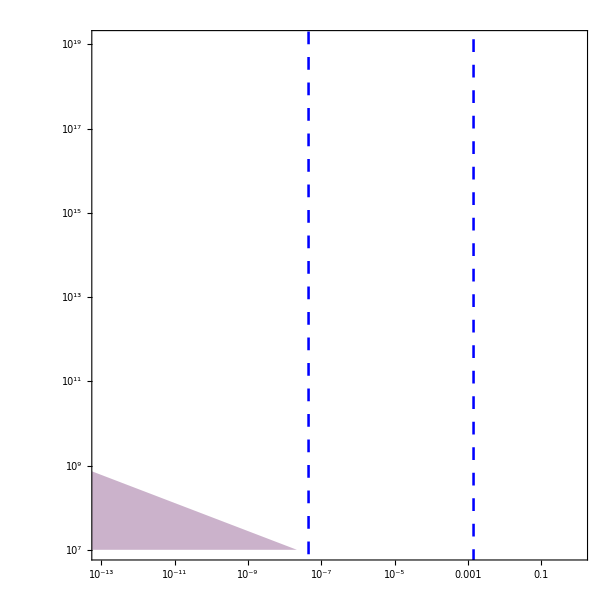

```mathematica
unstablePlot=LogLogPlot[{fatx1},{meV,10^-16,10},
Evaluate[mysty],
AspectRatio->1,
PlotStyle->{Directive[Opacity[0]]},
Filling->{1->Bottom},
FillingStyle->Directive[Opacity[0.3],Darker[Purple]],
PlotRange->{{mmin,mmax},{fmin,fmax}},
FrameTicks->{{logticks1,Automatic},{logticks2,Automatic}},
FrameLabel->{
MaTeX["m_\\phi\\, \\rm{[eV]}",Magnification->frameLabelSize],
MaTeX["f\\, \\rm{[GeV]}",Magnification->frameLabelSize]},
GridLines->Full,
GridLinesStyle->Opacity[0.1],
FrameTicksStyle->Directive[frameticksSize],
Epilog-> {{Directive[Blue,Dashing[0.015],Thickness[linethickness]],line1,line2,line3}}]
```

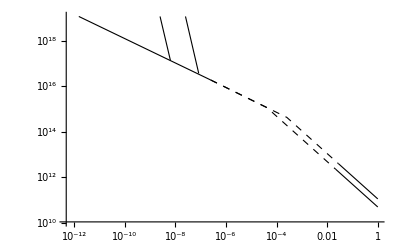

```mathematica
rlxnPlot=ListLogLogPlot[{RDMsolid100Min,
RDMsolid246Min,
RDMsolidDP,
RDMsolid100DP,
RDMsolid246DP,
RDMdashed100Min,
RDMdashed246Min},
Joined->True,
PlotStyle->{Directive[Black,Thickness[thinlinethickness]],
Directive[Black,Thickness[thinlinethickness]],
Directive[Black,Thickness[thinlinethickness]],
Directive[Black,Thickness[thinlinethickness]],
Directive[Black,Thickness[thinlinethickness]],
Directive[Black,Dashed,Thickness[thinlinethickness]],
Directive[Black,Dashed,Thickness[thinlinethickness]]}]
```

#### The Figure

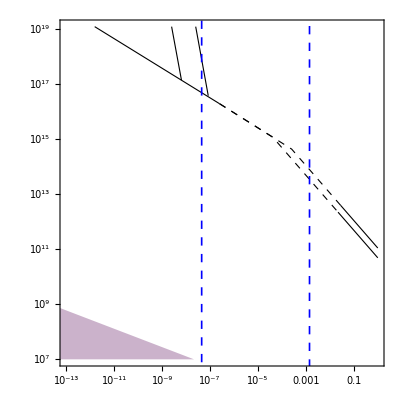

```mathematica
Show[unstablePlot,rlxnPlot]
```

### Plot R_⋆ vs M_⋆. Contours for encounter rate, overdensity, and stable axion stars

#### Range

```mathematica
ticks1=Table[{10^(1+4k),Superscript[10,1+4k]},{k,-2,10}];
ticks2=Table[{10^(2k),Superscript[10,2k]},{k,-2,10}];

(* Plot range options *)
MPlotmin=1;
MPlotmax=10^19;

RPlotmin=10;
RPlotmax=10^11;
```

#### Separate Plots

```mathematica
circledStar=Module[{color,thick,circle,pentagonPts,innerPt,starPts,star},color=Black;
thick=Scaled[.001];
pentagonPts=CirclePoints[5];
innerPt=RegionIntersection[Line[{pentagonPts[[1]],pentagonPts[[3]]}],Line[{pentagonPts[[2]],pentagonPts[[4]]}]];
starPts=N[DeleteDuplicates[Catenate[NestList[RotationTransform[360/5 Degree],{pentagonPts[[2]],innerPt[[1,1]],pentagonPts[[3]]},4]]]]/.{a1_,b1_}->{.7a1+17.8,.7 .5 b1+11.3};
star={EdgeForm[{Thickness[thick],Red}],FaceForm[color],Polygon[starPts]};
Graphics[{star}]]//Quiet;
```

```mathematica
pMRmass[meVsub_]:=LogLogPlot[RkmASt[meVsub,Mkg],
{Mkg,10,10^30},
PlotRange->{{MPlotmin,MPlotmax},{RPlotmin,RPlotmax}},
PlotStyle->Directive[Black,Dotted,Thickness[thinlinethickness]],#]&[mysty]
```

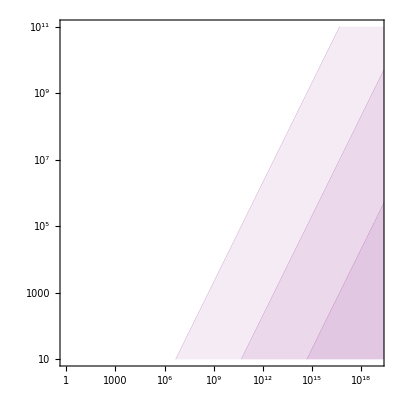

```mathematica
unstableMRPlot=LogLogPlot[{RkmUNSTABLE[10^6,Mkg],
RkmUNSTABLE[10^8,Mkg],
RkmUNSTABLE[10^10,Mkg]},
{Mkg,1,10^30},
GridLines->Full,
GridLinesStyle->Opacity[0.1],
AspectRatio->1,
PlotStyle->Directive[Thickness[0.0001],Purple],
Filling->{
{1->{Bottom,{Opacity[0],{Purple,Opacity[.08]}}}},
{2->{Bottom,{Opacity[0],{Purple,Opacity[.08]}}}},
{3->{Bottom,{Opacity[0],{Purple,Opacity[.08]}}}}},
FillingStyle->{Opacity[0.4],Opacity[0.3],Opacity[0.2],Opacity[0.1]},
FrameLabel->{
MaTeX["M_{\\star}\\, [\\rm{kg}]",Magnification->frameLabelSize],
MaTeX["R_\\star\\, [\\rm{km}]",Magnification->frameLabelSize]},
FrameTicks->{
{ticks2,Automatic},
{ticks1,Automatic}},
FrameTicksStyle->frameticksSize,
PlotRange->{{MPlotmin,MPlotmax},{RPlotmin,RPlotmax}},#]&[mysty]
```

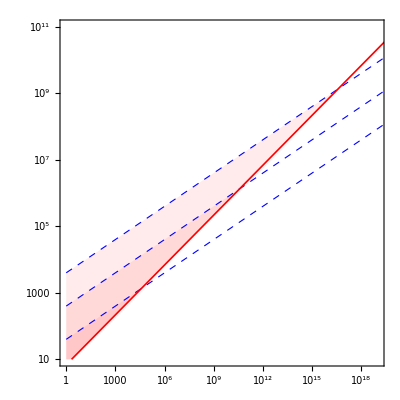

```mathematica
MRPlot=LogLogPlot[{RkmFIXρ[1 rlocalkgkm3,Mkg],
RkmFIXρ[10^3 rlocalkgkm3,Mkg],
RkmFIXρ[10^6 rlocalkgkm3,Mkg],
RkmFIXΓ[1.,Mkg]},
{Mkg,1,10^30},
GridLines->Full,
GridLinesStyle->Opacity[0.1],
AspectRatio->1,
PlotStyle->{
Directive[Blue,Dashed,Thickness[thinlinethickness]],
Directive[Blue,Dashed,Thickness[thinlinethickness]],
Directive[Blue,Dashed,Thickness[thinlinethickness]],
Directive[Red,Thick,Thickness[linethickness]]},
Filling->{1->{{4},{Opacity[0],{Red,Opacity[.08]}}},
{2->{{4},{Opacity[0],{Red,Opacity[.08]}}}},
{3->{{4},{Opacity[0],{Red,Opacity[.08]}}}}},
FillingStyle->{
Opacity[0.4],
Opacity[0.3],
Opacity[0.2],
Opacity[0.1]},
FrameLabel->{
MaTeX["M_{\\star}\\, [\\rm{kg}]",Magnification->frameLabelSize],
MaTeX["R_\\star\\, [\\rm{km}]",Magnification->frameLabelSize]},
FrameTicks->{{ticks2,Automatic},{ticks1,Automatic}},
FrameTicksStyle->frameticksSize,
PlotRange->{{MPlotmin,MPlotmax},{RPlotmin,RPlotmax}},#]&[mysty]
```

#### The Figure

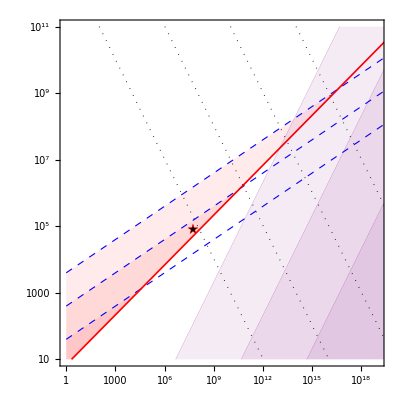

```mathematica
Show[MRPlot,
unstableMRPlot,
pMRmass[10^-1],
pMRmass[10^-3],
pMRmass[10^-5],
pMRmass[10^-7],
circledStar]
```

## Maximal Gravitational Atom

#### Range

```mathematica
(* Plot range options *)
mmin=10^-17;
mmax=10^-7;
```

### Maximum mass M_max vs m_ϕ (solar and Earth-bound)

#### Separate Plots

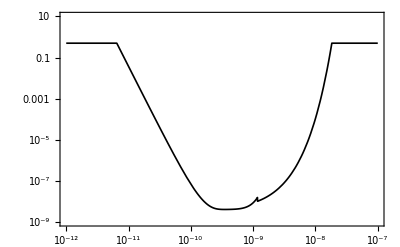

```mathematica
MEplot=LogLogPlot[{MmaxEarth[meV]/ME},{meV,10^-12,mmax},
PlotRange->{{10^-12,mmax},{10^-9,10}},
PlotStyle->{
{Thickness[0.003],Black}},
Exclusions->None,
FrameTicks->{{ticksEven,ticksNoLabel},{ticksOdd,ticksNoLabel}},
FrameTicksStyle->Thin,
FrameLabel->{
tex15["m_\\phi\\,\\,[\\rm eV]"],
tex15["M_\\star/M_{\\rm ext}"]},
#]&[mysty]
```

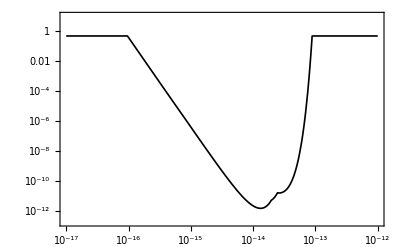

```mathematica
MSplot=LogLogPlot[{MmaxSun[meV]/Msun},{meV,mmin,10^-12},
PlotRange->{{mmin,10^-12},{2 10^-13,10}},
PlotStyle->{
{Thickness[0.003],Black}},
Exclusions->None,
FrameTicks->{{ticksEven,ticksNoLabel},{ticksOdd,ticksNoLabel}},
FrameTicksStyle->Thin,
FrameLabel->{
tex15["m_\\phi\\,\\,[\\rm eV]"],
tex15["M_\\star/M_{\\rm ext}"]},
#]&[mysty]
```

#### The Figure

```mathematica
astroPlt=LogLogPlot[{MstarCut},{meV,mmin,mmax},
PlotRange->{{mmin,mmax},{10^-13,10}},
PlotStyle->Directive[Thickness[0.001],Gray],
Exclusions->None,
FrameTicks->{{ticksEven,ticksNoLabel},{ticksOdd,ticksNoLabel}},
FrameTicksStyle->Thin,
Filling->{1->Top},
FillingStyle->Opacity[0.5,Gray],
FrameLabel->{
tex15["m_\\phi\\,\\,[\\rm eV]"],
tex15["M_\\star/M_{\\rm ext}"]},
#]&[mysty];

txt1=Graphics[Text[Rotate[tex["M_{\\rm ext} = M_\\oplus",1],-69Degree],{-23.5,-10}]];
txt2=Graphics[Text[Rotate[tex["M_{\\rm ext} = M_\\odot",1],-69Degree],{-34.6,-10}]];
Show[astroPlt,MEplot,MSplot,txt1 ,txt2,ImageSize->350]
```

-Graphics-

### Maximum density ρ_⋆ vs m_ϕ (solar and Earth-bound)

#### Separate Plots

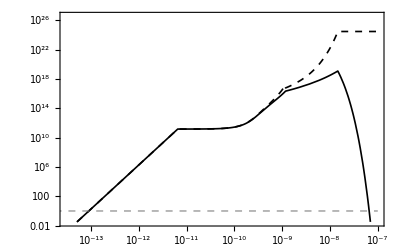

```mathematica
rhoEHPlt=LogLogPlot[{
rhoEarth[meV,Min[MmaxEarth[meV],(RhaloEarth[meV]/RE)^3 ME/2] ,RE]/rlocal,
rhoEarth[meV,Min[MmaxEarth[meV],(RhaloEarth[meV]/RE)^3 ME/2] ,0]/rlocal,
1},{meV,mmin,mmax},
PlotRange->{{(*mmin*)3 10^-14,mmax},{10^-43/rlocal,10^-15/rlocal}},
FrameLabel->{
tex["m_\\phi\\,\\,[\\rm eV]",1.5],
tex["\\rho_\\star/\\rho_{\\rm local}",1.5]},
PlotStyle->{
{Black,Thickness[0.003]},
{Black,Dashed,Thickness[0.003]},
{Gray,Dashed,Thickness[0.002],Opacity[1]}},
FrameTicks->{Automatic,{ticksEven,ticksNoLabel}},
FrameTicksStyle->Directive[Thin,12],
#]&[mysty]
```

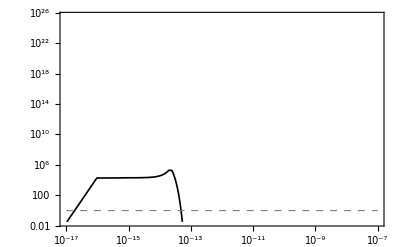

```mathematica
rhoSHPlt=LogLogPlot[{
rhoSun[meV,Min[MmaxSun[meV],(RhaloSun[meV]/Rsun)^3 Msun/2] ,aPlanets⟦3⟧]/rlocal,1},{meV,mmin,mmax},
PlotRange->{{mmin,mmax},{10^-43/rlocal,10^-16/rlocal}},
FrameLabel->{tex["m_\\phi\\,\\,[\\rm eV]",1.5],tex["\\rho_\\star/\\rho_{\\rm local}",1.5]},
PlotStyle->{{Black,Thickness[0.003]},
{Gray,Dashed,Thickness[0.002],Opacity[1]}},
FrameTicks->{Automatic,{ticksEven,ticksNoLabel}},
FrameTicksStyle->Directive[Thin,12],
#]&[mysty]
```

#### The Figure

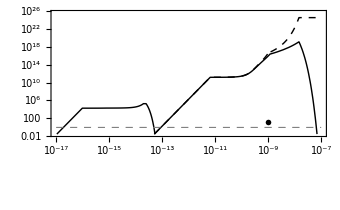

```mathematica
txtLocal=Graphics[Text[tex["\\color{gray} \\rho_\\star/\\rho_{\\rm local}=1",1.1],{10^-9,2 10^1}//Log]];
txtEarth=Graphics[Text[Rotate["Captured by Earth",59Degree],{-27.3,-85}]];
txtSun=Graphics[Text[Rotate["by Sun",61Degree],{-37.1,-92}]];

Show[rhoSHPlt,rhoEHPlt,txtLocal,txtEarth,txtSun,ImageSize->340]
```

### Maximum field value ϕ vs m_ϕ (solar and Earth-bound)

#### Separate Plots

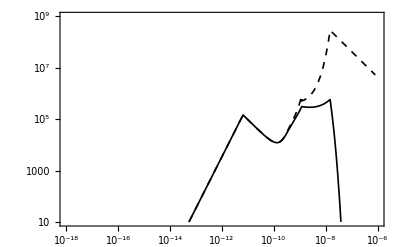

```mathematica
phiEHPlt=LogLogPlot[{
phiHaloProfileEarth[meV,Min[MmaxEarth[meV],(RhaloEarth[meV]/RE)^3 ME/2] ,0],
phiHaloProfileEarth[meV,Min[MmaxEarth[meV],(RhaloEarth[meV]/RE)^3 ME/2] ,RE]},{meV,mmin,mmax},
PlotRange->{{mmin,mmax},{10^1,10^9}},
FrameLabel->{tex["m_\\phi\\,\\,[\\rm eV]",1.5],tex["\\phi \\,\\,[\\rm GeV]",1.5]},
PlotStyle->{
{Black,Dashed,Thickness[0.003]},
{Black,Thickness[0.003]}},
FrameTicks->{{ticksOdd,ticksNoLabel},{ticksEven,ticksNoLabel}},
FrameTicksStyle->Directive[Thin,12],
#]&[mysty]
```

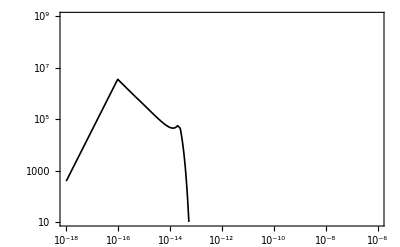

```mathematica
phiSHPlt=LogLogPlot[{
phiHaloProfileSun[meV,Min[MmaxSun[meV],(RhaloSun[meV]/Rsun)^3 Msun/2] ,aPlanets⟦3⟧]},{meV,mmin,mmax},
PlotRange->{{mmin,mmax},{10^1,10^9}},
FrameLabel->{
tex["m_\\phi\\,\\,[\\rm eV]",1.5],
tex["\\phi \\,\\,[\\rm GeV]",1.5]},
PlotStyle->{
{Black,Thickness[0.003]},
{Gray,Dashed,Thickness[0.002]}},
FrameTicks->{{ticksOdd,ticksNoLabel},{ticksEven,ticksNoLabel}},
FrameTicksStyle->Directive[Thin,12],
#]&[mysty]
```

#### The Figure

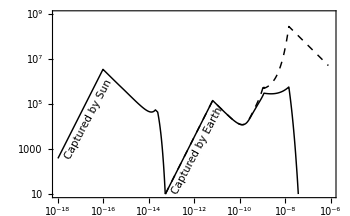

```mathematica
txtEarth2=Graphics[Text[Style[Rotate["Captured by Earth",62Degree],10.5],{-27.3,6.7}]];
txtSun2=Graphics[Text[Style[Rotate["Captured by Sun",62Degree],10.5],{-38.4,10}]];

Show[phiEHPlt,phiSHPlt,txtEarth2,txtSun2,ImageSize->350]
```

## Earth-Bound Gravitational Atom Radius

#### Range

```mathematica
(* Plot range options *)
mmin=10^-13;
mmax=10^-5;
```

#### The Figure

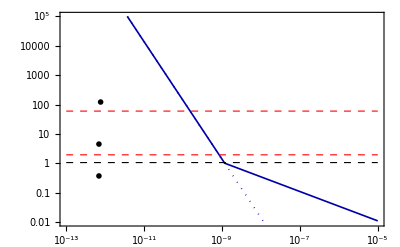

```mathematica
RPlot=LogLogPlot[{RhaloEarth[meV]/RE,RhaloNaive[meV,ME]/ RE,1.05,RMoon/RE,RLAGEOS/RE},{meV,mmin,mmax},
PlotStyle->{
{Darker[Blue],Thickness[0.003]},
{Darker[Blue],Thickness[0.003],Dotted},
{Dashed,Black,Thickness[0.002]},
{Dashed,Red,Thickness[0.002]},
{Dashed,Red,Thickness[0.002]}},
PlotRange->{{mmin,mmax},{10^-2,10^5}},
Exclusions->None,
FrameLabel->{tex["m_\\phi\\,\\,[\\rm eV]",1.5],tex["R_\\star/R_\\oplus",1.5]},
FrameTicksStyle->13,
FrameTicks->{{ticksEven,ticksNoLabel},{ticksEven,ticksNoLabel}},
#]&[mysty];

tmp0=Graphics[Text[tex["R_\\star=R_\\oplus",1],{-28.,-1}]];
tmp1=Graphics[Text[tex["R_\\star=R_{\\rm L}",1],{-28,1.5}]];
tmp2=Graphics[Text[tex["R_\\star=R_{\\rm M}",1],{-27.9,4.8}]];
Show[RPlot,tmp0,tmp1,tmp2]

Clear[mmin,mmax,tmp0,tmp1,tmp2]
```